```mathematica
(* Aquí vamos a hacer indicadores bursátiles globales por sector. Empezaremos con los 25 sectores más importantes por MarketCap *)
```

```mathematica
(* No hay marketcap para todos los activos. Supongo que habrá algunos en distintas monedas, veamos cómo nos lo da el programa. Vamos a pedir que nos ordenen los sectores por MarketCap (aunque sea solamente indicativo de las bolsas americanas, que son las que más lo publican).
```

```mathematica
mktcap[sec_]:=Sort[{sec,Total[DeleteCases[FinancialData[#, "MarketCap"]&/@FinancialData[sec, "Name"],_Missing]]},#1[[2]]>#2[[2]]&]
```

```mathematica
sectors=FinancialData["Sectors", "Members"];
```

```mathematica
(*Vamos a tener que hacerlo por grupos pequeños, de 12-15 sectores *)
```

```mathematica
seclice=sectors[[#;;179;;15]]&/@Table[i,{i,1,15}];
```

```mathematica
Dimensions[seclice[[#]]]&/@Table[i,{i,1,15}]
```

{{12},{12},{12},{12},{12},{12},{12},{12},{12},{12},{12},{12},{12},{12},{11}}

```mathematica
Total@Flatten[%]
```

179

```mathematica
mk[x_]:=mktcap[#]&/@seclice[[x]];
```

```mathematica
mk[1]
```

FinancialData::notent: NASDAQ:MGNI is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NYSE:DMS is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Part::partd: Part specification AdvertisingAgencies⟦2⟧ is longer than depth of object.

FinancialData::notent: NASDAQ:ALTA is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

Part::partd: Part specification BanksRegional⟦2⟧ is longer than depth of object.

Part::partd: Part specification BusinessEquipment⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{AdvertisingAgencies,3.974723515473677e10 $},{BanksRegional,1.0041985493099401e12 $},{BusinessEquipment,0},{Copper,9.040253477595956e10 $},{ElectronicsDistribution,0},{HealthInformationServices,1.1140294956312589e11 $},{IntegratedFreightAndLogistics,2.8947162966451196e11 $},{MedicalDistribution,7.8282621576752e10 $},{PayTV,0},{REITMortgage,4.58054710257207e10 $},{ShellCompanies,1.909977349693675e10 $},{TextileManufacturing,2.1040285891443908e9 $}}

```mathematica
mk[2]
```

Part::partd: Part specification AerospaceAndDefense⟦2⟧ is longer than depth of object.

Part::partd: Part specification BanksRegionalAsia⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: NYSE:SOS is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:13N1 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:LD62 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{AerospaceAndDefense,5.347503210676238e11 $},{BanksRegionalAsia,0},{BusinessEquipmentAndSupplies,1.782864854988666e10 $},{CreditServices,1.272912466717272e12 $},{EngineeringAndConstruction,1.2104077518476158e11 $},{HomeFurnishingsAndFixtures,0},{IntegratedShippingAndLogistics,0},{MedicalInstrumentsAndSupplies,4.1617912106345984e11 $},{PersonalServices,5.60116833586374e10 $},{REITOffice,1.3337347144366325e11 $},{ShippingAndPorts,0},{ThermalCoal,1.9973479915992284e9 $}}

```mathematica
mk[3]
```

Part::partd: Part specification AgriculturalInputs⟦2⟧ is longer than depth of object.

Part::partd: Part specification BanksRegionalEurope⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{AgriculturalInputs,1.1598548912712141e11 $},{BanksRegionalEurope,0},{BusinessServices,0},{DataStorage,0},{Entertainment,1.0451032247830286e12 $},{HomeImprovementRetail,4.257701240067477e11 $},{InternetContentAndInformation,3.4877074498176797e12 $},{MetalFabrication,1.1988707919976831e10 $},{PharmaceuticalRetailers,3.5544821888810036e10 $},{REITResidential,1.6575755618743512e11 $},{Silver,3.259095900689933e10 $},{Tobacco,2.8602945239443274e11 $}}

```mathematica
mk[4]
```

Part::partd: Part specification Airlines⟦2⟧ is longer than depth of object.

Part::partd: Part specification BanksRegionalLatinAmerica⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: NASDAQ:SNEX is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NYSE:GOED is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

{{Airlines,1.1666350661755774e11 $},{BanksRegionalLatinAmerica,0},{CapitalMarkets,3.702771114810601e11 $},{DepartmentStores,1.239142233760873e10 $},{FarmAndConstructionEquipment,0},{HomeImprovementStores,0},{InternetRetail,2.8033600529318564e12 $},{MortgageFinance,3.625938828991914e10 $},{PollutionAndTreatmentControls,5.290849186658317e9 $},{REITRetail,1.1468359813514742e11 $},{SoftwareApplication,1.6962058245988794e12 $},{ToolsAndAccessories,5.835764711294168e10 $}}

```mathematica
mk[5]
```

Part::partd: Part specification AirportsAndAirServices⟦2⟧ is longer than depth of object.

Part::partd: Part specification BanksRegionalUS⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:JP1A is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:C3IA is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

{{AirportsAndAirServices,1.7767910698538254e10 $},{BanksRegionalUS,0},{Chemicals,2.079473629910349e11 $},{DiagnosticsAndResearch,7.162292108431948e11 $},{FarmAndHeavyConstructionMachinery,2.1594733104793124e11 $},{HouseholdAndPersonalProducts,9.384550130872661e11 $},{Leisure,7.183759292586916e10 $},{OilAndGasDrilling,1.7849242278279675e10 $},{Publishing,6.3812977046265945e10 $},{REITSpecialty,3.459925425922069e11 $},{SoftwareInfrastructure,2.6536668870738354e12 $},{TravelServices,1.5207794715829895e11 $}}

```mathematica
mk[6]
```

Part::partd: Part specification Aluminum⟦2⟧ is longer than depth of object.

Part::partd: Part specification BeveragesBrewers⟦2⟧ is longer than depth of object.

Part::partd: Part specification Coal⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: NYSE:CRCQQ is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NASDAQ:CVLG is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

{{Aluminum,9.325207741073837e9 $},{BeveragesBrewers,3.076412706854275e11 $},{Coal,0},{DiscountStores,7.356087290631287e11 $},{FarmProducts,6.276466737014667e10 $},{IndustrialDistribution,9.840432953082959e10 $},{Lodging,1.083727594303914e11 $},{OilAndGasEAndP,4.2830625933881616e11 $},{Railroads,5.514584383454027e11 $},{RentalAndLeasingServices,5.4871798250819275e10 $},{Solar,4.0812860131095024e10 $},{Trucking,5.023034766267105e10 $}}

```mathematica
mk[7]
```

FinancialData::notent: F:RYAA is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:SQC is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Part::partd: Part specification ApparelManufacturing⟦2⟧ is longer than depth of object.

Part::partd: Part specification BeveragesNonAlcoholic⟦2⟧ is longer than depth of object.

Part::partd: Part specification CokingCoal⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:KX4A is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{ApparelManufacturing,8.479823082446191e10 $},{BeveragesNonAlcoholic,5.432524010782399e11 $},{CokingCoal,1.7778023143547113e9 $},{DiversifiedIndustrials,0},{FinancialConglomerates,1.3194408139557804e10 $},{IndustrialMetalsAndMinerals,0},{LongTermCareFacilities,0},{OilAndGasEquipmentAndServices,9.272511342216908e10 $},{RealEstateDevelopment,7.923505679751064e9 $},{ResidentialConstruction,1.2373914223078624e11 $},{SpecialtyBusinessServices,1.3379144201633968e11 $},{Uranium,1.3806912287453716e10 $}}

```mathematica
mk[8]
```

Part::partd: Part specification ApparelRetail⟦2⟧ is longer than depth of object.

Part::partd: Part specification BeveragesSoftDrinks⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:P0T2 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NASDAQ:CXDO is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: PA:S30 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{ApparelRetail,1.954861080765644e11 $},{BeveragesSoftDrinks,0},{CommunicationEquipment,3.514240824711964e11 $},{DrugManufacturersGeneral,2.0606200316944834e12 $},{FinancialDataAndStockExchanges,3.3611320459332544e11 $},{InformationTechnologyServices,7.765632233459078e11 $},{LumberAndWoodProduction,2.488273351028694e10 $},{OilAndGasIntegrated,1.1663741507185312e12 $},{RealEstateDiversified,5.687547246203833e9 $},{ResortsAndCasinos,1.1128209133654616e11 $},{SpecialtyChemicals,4.226286244673747e11 $},{UtilitiesDiversified,3.4052959108108e11 $}}

```mathematica
mk[9]
```

Part::partd: Part specification ApparelStores⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

Part::partd: Part specification BeveragesWineriesAndDistilleries⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{ApparelStores,0},{BeveragesWineriesAndDistilleries,2.2634143608391064e11 $},{ComputerDistribution,0},{DrugManufacturersMajor,0},{FoodDistribution,4.4782254938553665e10 $},{InfrastructureOperations,2.3264380576389008e9 $},{LuxuryGoods,2.0614233909646732e10 $},{OilAndGasMidstream,5.36081410277813e11 $},{RealEstateGeneral,0},{Restaurants,4.9695071753851337e11 $},{SpecialtyFinance,0},{UtilitiesIndependentPowerProducers,3.556324013556535e10 $}}

```mathematica
mk[10]
```

Part::partd: Part specification AssetManagement⟦2⟧ is longer than depth of object.

FinancialData::notent: F:I9S1 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:PMRA is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Part::partd: Part specification Biotechnology⟦2⟧ is longer than depth of object.

Part::partd: Part specification ComputerHardware⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:135A is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{AssetManagement,7.905465821364834e11 $},{Biotechnology,8.299925869494489e11 $},{ComputerHardware,1.6307803873537976e11 $},{DrugManufacturersSpecialtyAndGeneric,2.8526955464423126e11 $},{FootwearAndAccessories,1.969412113897934e11 $},{InsuranceBrokers,1.8125831249012964e11 $},{MarineShipping,1.237280203430637e10 $},{OilAndGasRefiningAndMarketing,1.0536316383861731e11 $},{RealEstateServices,1.1724705761551123e11 $},{RubberAndPlastics,0},{SpecialtyIndustrialMachinery,8.21012595467512e11 $},{UtilitiesRegulatedElectric,6.855269160102974e11 $}}

```mathematica
mk[11]
```

Part::partd: Part specification AutoAndTruckDealerships⟦2⟧ is longer than depth of object.

Part::partd: Part specification Broadcasting⟦2⟧ is longer than depth of object.

Part::partd: Part specification ComputerSystems⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:DFPP is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: TO:GENM is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: DE:ODP1 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{AutoAndTruckDealerships,4.373196192744281e10 $},{Broadcasting,1.4996491855534503e11 $},{ComputerSystems,0},{EducationAndTrainingServices,9.907912619889105e10 $},{FurnishingsFixturesAndAppliances,4.962046603595041e10 $},{InsuranceDiversified,1.235712952370337e12 $},{MarketingServices,0},{OtherIndustrialMetalsAndMining,4.771124691748744e11 $},{RecreationalVehicles,3.903062818650463e10 $},{SavingsAndCooperativeBanks,0},{SpecialtyRetail,2.3820716303438324e11 $},{UtilitiesRegulatedGas,6.529963905638729e10 $}}

```mathematica
mk[12]
```

Part::partd: Part specification AutoManufacturers⟦2⟧ is longer than depth of object.

Part::partd: Part specification BroadcastingRadio⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: AMEX:ITRG is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:DXZB is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:GFX1 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{AutoManufacturers,7.965018220732725e11 $},{BroadcastingRadio,0},{Confectioners,1.1643859783851413e11 $},{ElectricalEquipmentAndParts,9.486674182869504e10 $},{Gambling,1.6849322412414057e10 $},{InsuranceLife,3.675890146003295e11 $},{MediaDiversified,0},{OtherPreciousMetalsAndMining,2.3638789916356834e10 $},{REITDiversified,8.34535115313242e10 $},{ScientificAndTechnicalInstruments,1.3480487382385959e11 $},{StaffingAndEmploymentServices,1.2433503747585979e11 $},{UtilitiesRegulatedWater,5.124520019367154e10 $}}

```mathematica
mk[13]
```

Part::partd: Part specification AutoParts⟦2⟧ is longer than depth of object.

Part::partd: Part specification BroadcastingTV⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:5RN1 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: F:T23A is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: TO:BNAU is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{AutoParts,1.405857024574129e11 $},{BroadcastingTV,0},{Conglomerates,2.2394593203890533e10 $},{ElectronicComponents,1.279717712007015e11 $},{Gold,6.41819478467224e11 $},{InsurancePropertyAndCasualty,3.3588987496203613e11 $},{MedicalCare,0},{PackagedFoods,3.456794474497269e11 $},{REITHealthcareFacilities,9.857596597974342e10 $},{SecurityAndProtectionServices,3.152804141662598e10 $},{StaffingAndOutsourcingServices,0},{UtilitiesRenewable,7.079340680833932e10 $}}

```mathematica
mk[14]
```

FinancialData::notent: L:NWG is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NYSE:NWG is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Part::partd: Part specification BanksDiversified⟦2⟧ is longer than depth of object.

Part::partd: Part specification BuildingMaterials⟦2⟧ is longer than depth of object.

Part::partd: Part specification ConsultingServices⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:F0O3 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{{BanksDiversified,2.2775684918556848e13 $},{BuildingMaterials,8.600177431209633e10 $},{ConsultingServices,2.1488862480170273e11 $},{ElectronicGamingAndMultimedia,2.0460428697334656e11 $},{GroceryStores,2.0724842723256128e11 $},{InsuranceReinsurance,2.3952045464332947e10 $},{MedicalCareFacilities,1.618019858289657e11 $},{PackagingAndContainers,1.3849745762422046e11 $},{REITHotelAndMotel,2.8525127336109978e10 $},{SemiconductorEquipmentAndMaterials,3.5032233927787744e11 $},{Steel,8.249229703314981e10 $},{WasteManagement,1.552119594445667e11 $}}

```mathematica
mk[15]
```

Part::partd: Part specification BanksGlobal⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

Part::partd: Part specification BuildingProductsAndEquipment⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FinancialData::notent: F:51KB is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NASDAQ:SRGA is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

{{BanksGlobal,0},{BuildingProductsAndEquipment,8.159248072995203e10 $},{ConsumerElectronics,2.1759268617051875e12 $},{ElectronicsAndComputerDistribution,1.6506323389437515e10 $},{HealthcarePlans,6.068443083205991e11 $},{InsuranceSpecialty,4.324374879853093e10 $},{MedicalDevices,6.892186303603368e11 $},{PaperAndPaperProducts,1.6688822778834929e10 $},{REITIndustrial,1.9082221495174902e11 $},{Semiconductors,1.8285307862186348e12 $},{TelecomServices,1.4869406229654658e12 $}}

```mathematica
(* Aquí tenemos que confiar en los % almacenados en la memoria temporal del cuaderno. Los %# de esta lista por alguna razón no jalan con Table. Hay que checar que los números cuadren *)
```

```mathematica
Clear[l,m,h,i]
```

```mathematica
l=Join[{%34,%35,%36,%37,%38,%39,%40,%41,%42,%43,%44,%45,%46,%47,%48}];
```

```mathematica
m=Flatten[l,1];
```

```mathematica
n=Reverse@SortBy[m,Last];
```

```mathematica
n//TableForm
```

BanksDiversified | 2.2775684918556848e13 $
InternetContentAndInformation | 3.4877074498176797e12 $
InternetRetail | 2.8033600529318564e12 $
SoftwareInfrastructure | 2.6536668870738354e12 $
ConsumerElectronics | 2.1759268617051875e12 $
DrugManufacturersGeneral | 2.0606200316944834e12 $
Semiconductors | 1.8285307862186348e12 $
SoftwareApplication | 1.6962058245988794e12 $
TelecomServices | 1.4869406229654658e12 $
CreditServices | 1.272912466717272e12 $
InsuranceDiversified | 1.235712952370337e12 $
OilAndGasIntegrated | 1.1663741507185312e12 $
Entertainment | 1.0451032247830286e12 $
BanksRegional | 1.0041985493099401e12 $
HouseholdAndPersonalProducts | 9.384550130872661e11 $
Biotechnology | 8.299925869494489e11 $
SpecialtyIndustrialMachinery | 8.21012595467512e11 $
AutoManufacturers | 7.965018220732725e11 $
AssetManagement | 7.905465821364834e11 $
InformationTechnologyServices | 7.765632233459078e11 $
DiscountStores | 7.356087290631287e11 $
DiagnosticsAndResearch | 7.162292108431948e11 $
MedicalDevices | 6.892186303603368e11 $
UtilitiesRegulatedElectric | 6.855269160102974e11 $
Gold | 6.41819478467224e11 $
HealthcarePlans | 6.068443083205991e11 $
Railroads | 5.514584383454027e11 $
BeveragesNonAlcoholic | 5.432524010782399e11 $
OilAndGasMidstream | 5.36081410277813e11 $
AerospaceAndDefense | 5.347503210676238e11 $
Restaurants | 4.9695071753851337e11 $
OtherIndustrialMetalsAndMining | 4.771124691748744e11 $
OilAndGasEAndP | 4.2830625933881616e11 $
HomeImprovementRetail | 4.257701240067477e11 $
SpecialtyChemicals | 4.226286244673747e11 $
MedicalInstrumentsAndSupplies | 4.1617912106345984e11 $
CapitalMarkets | 3.702771114810601e11 $
InsuranceLife | 3.675890146003295e11 $
CommunicationEquipment | 3.514240824711964e11 $
SemiconductorEquipmentAndMaterials | 3.5032233927787744e11 $
REITSpecialty | 3.459925425922069e11 $
PackagedFoods | 3.456794474497269e11 $
UtilitiesDiversified | 3.4052959108108e11 $
FinancialDataAndStockExchanges | 3.3611320459332544e11 $
InsurancePropertyAndCasualty | 3.3588987496203613e11 $
BeveragesBrewers | 3.076412706854275e11 $
IntegratedFreightAndLogistics | 2.8947162966451196e11 $
Tobacco | 2.8602945239443274e11 $
DrugManufacturersSpecialtyAndGeneric | 2.8526955464423126e11 $
SpecialtyRetail | 2.3820716303438324e11 $
BeveragesWineriesAndDistilleries | 2.2634143608391064e11 $
FarmAndHeavyConstructionMachinery | 2.1594733104793124e11 $
ConsultingServices | 2.1488862480170273e11 $
Chemicals | 2.079473629910349e11 $
GroceryStores | 2.0724842723256128e11 $
ElectronicGamingAndMultimedia | 2.0460428697334656e11 $
FootwearAndAccessories | 1.969412113897934e11 $
ApparelRetail | 1.954861080765644e11 $
REITIndustrial | 1.9082221495174902e11 $
InsuranceBrokers | 1.8125831249012964e11 $
REITResidential | 1.6575755618743512e11 $
ComputerHardware | 1.6307803873537976e11 $
MedicalCareFacilities | 1.618019858289657e11 $
WasteManagement | 1.552119594445667e11 $
TravelServices | 1.5207794715829895e11 $
Broadcasting | 1.4996491855534503e11 $
AutoParts | 1.405857024574129e11 $
PackagingAndContainers | 1.3849745762422046e11 $
ScientificAndTechnicalInstruments | 1.3480487382385959e11 $
SpecialtyBusinessServices | 1.3379144201633968e11 $
REITOffice | 1.3337347144366325e11 $
ElectronicComponents | 1.279717712007015e11 $
StaffingAndEmploymentServices | 1.2433503747585979e11 $
ResidentialConstruction | 1.2373914223078624e11 $
EngineeringAndConstruction | 1.2104077518476158e11 $
RealEstateServices | 1.1724705761551123e11 $
Airlines | 1.1666350661755774e11 $
Confectioners | 1.1643859783851413e11 $
AgriculturalInputs | 1.1598548912712141e11 $
REITRetail | 1.1468359813514742e11 $
HealthInformationServices | 1.1140294956312589e11 $
ResortsAndCasinos | 1.1128209133654616e11 $
Lodging | 1.083727594303914e11 $
OilAndGasRefiningAndMarketing | 1.0536316383861731e11 $
EducationAndTrainingServices | 9.907912619889105e10 $
REITHealthcareFacilities | 9.857596597974342e10 $
IndustrialDistribution | 9.840432953082959e10 $
ElectricalEquipmentAndParts | 9.486674182869504e10 $
OilAndGasEquipmentAndServices | 9.272511342216908e10 $
Copper | 9.040253477595956e10 $
BuildingMaterials | 8.600177431209633e10 $
ApparelManufacturing | 8.479823082446191e10 $
REITDiversified | 8.34535115313242e10 $
Steel | 8.249229703314981e10 $
BuildingProductsAndEquipment | 8.159248072995203e10 $
MedicalDistribution | 7.8282621576752e10 $
Leisure | 7.183759292586916e10 $
UtilitiesRenewable | 7.079340680833932e10 $
UtilitiesRegulatedGas | 6.529963905638729e10 $
Publishing | 6.3812977046265945e10 $
FarmProducts | 6.276466737014667e10 $
ToolsAndAccessories | 5.835764711294168e10 $
PersonalServices | 5.60116833586374e10 $
RentalAndLeasingServices | 5.4871798250819275e10 $
UtilitiesRegulatedWater | 5.124520019367154e10 $
Trucking | 5.023034766267105e10 $
FurnishingsFixturesAndAppliances | 4.962046603595041e10 $
REITMortgage | 4.58054710257207e10 $
FoodDistribution | 4.4782254938553665e10 $
AutoAndTruckDealerships | 4.373196192744281e10 $
InsuranceSpecialty | 4.324374879853093e10 $
Solar | 4.0812860131095024e10 $
AdvertisingAgencies | 3.974723515473677e10 $
RecreationalVehicles | 3.903062818650463e10 $
MortgageFinance | 3.625938828991914e10 $
UtilitiesIndependentPowerProducers | 3.556324013556535e10 $
PharmaceuticalRetailers | 3.5544821888810036e10 $
Silver | 3.259095900689933e10 $
SecurityAndProtectionServices | 3.152804141662598e10 $
REITHotelAndMotel | 2.8525127336109978e10 $
LumberAndWoodProduction | 2.488273351028694e10 $
InsuranceReinsurance | 2.3952045464332947e10 $
OtherPreciousMetalsAndMining | 2.3638789916356834e10 $
Conglomerates | 2.2394593203890533e10 $
LuxuryGoods | 2.0614233909646732e10 $
ShellCompanies | 1.909977349693675e10 $
OilAndGasDrilling | 1.7849242278279675e10 $
BusinessEquipmentAndSupplies | 1.782864854988666e10 $
AirportsAndAirServices | 1.7767910698538254e10 $
Gambling | 1.6849322412414057e10 $
PaperAndPaperProducts | 1.6688822778834929e10 $
ElectronicsAndComputerDistribution | 1.6506323389437515e10 $
Uranium | 1.3806912287453716e10 $
FinancialConglomerates | 1.3194408139557804e10 $
DepartmentStores | 1.239142233760873e10 $
MarineShipping | 1.237280203430637e10 $
MetalFabrication | 1.1988707919976831e10 $
Aluminum | 9.325207741073837e9 $
RealEstateDevelopment | 7.923505679751064e9 $
RealEstateDiversified | 5.687547246203833e9 $
PollutionAndTreatmentControls | 5.290849186658317e9 $
InfrastructureOperations | 2.3264380576389008e9 $
TextileManufacturing | 2.1040285891443908e9 $
ThermalCoal | 1.9973479915992284e9 $
CokingCoal | 1.7778023143547113e9 $
StaffingAndOutsourcingServices | 0
SpecialtyFinance | 0
ShippingAndPorts | 0
SavingsAndCooperativeBanks | 0
RubberAndPlastics | 0
RealEstateGeneral | 0
PayTV | 0
MedicalCare | 0
MediaDiversified | 0
MarketingServices | 0
LongTermCareFacilities | 0
IntegratedShippingAndLogistics | 0
IndustrialMetalsAndMinerals | 0
HomeImprovementStores | 0
HomeFurnishingsAndFixtures | 0
FarmAndConstructionEquipment | 0
ElectronicsDistribution | 0
DrugManufacturersMajor | 0
DiversifiedIndustrials | 0
DataStorage | 0
ComputerSystems | 0
ComputerDistribution | 0
Coal | 0
BusinessServices | 0
BusinessEquipment | 0
BroadcastingTV | 0
BroadcastingRadio | 0
BeveragesSoftDrinks | 0
BanksRegionalUS | 0
BanksRegionalLatinAmerica | 0
BanksRegionalEurope | 0
BanksRegionalAsia | 0
BanksGlobal | 0
ApparelStores | 0

```mathematica
o=Take[n,{1,25}]
```

{{SoftwareInfrastructure,2.6536668870738354e12 $},{SoftwareApplication,1.6962058245988794e12 $},{OilAndGasIntegrated,1.1663741507185312e12 $},{BanksRegional,1.0041985493099401e12 $},{InformationTechnologyServices,7.765632233459078e11 $},{Railroads,5.514584383454027e11 $},{BeveragesNonAlcoholic,5.432524010782399e11 $},{AerospaceAndDefense,5.347503210676238e11 $},{OilAndGasEAndP,4.2830625933881616e11 $},{SpecialtyChemicals,4.226286244673747e11 $},{REITSpecialty,3.459925425922069e11 $},{UtilitiesDiversified,3.4052959108108e11 $},{BeveragesBrewers,3.076412706854275e11 $},{DrugManufacturersSpecialtyAndGeneric,2.8526955464423126e11 $},{FootwearAndAccessories,1.969412113897934e11 $},{InsuranceBrokers,1.8125831249012964e11 $},{TravelServices,1.5207794715829895e11 $},{EngineeringAndConstruction,1.2104077518476158e11 $},{RealEstateServices,1.1724705761551123e11 $},{REITRetail,1.1468359813514742e11 $},{ResortsAndCasinos,1.1128209133654616e11 $},{Lodging,1.083727594303914e11 $},{OilAndGasRefiningAndMarketing,1.0536316383861731e11 $},{ApparelManufacturing,8.479823082446191e10 $},{Publishing,6.3812977046265945e10 $}}

```mathematica
Total[o]
```

{AerospaceAndDefense+ApparelManufacturing+BanksRegional+BeveragesBrewers+BeveragesNonAlcoholic+DrugManufacturersSpecialtyAndGeneric+EngineeringAndConstruction+FootwearAndAccessories+InformationTechnologyServices+InsuranceBrokers+Lodging+OilAndGasEAndP+OilAndGasIntegrated+OilAndGasRefiningAndMarketing+Publishing+Railroads+RealEstateServices+REITRetail+REITSpecialty+ResortsAndCasinos+SoftwareApplication+SoftwareInfrastructure+SpecialtyChemicals+TravelServices+UtilitiesDiversified,1.2413715762797422e13 $}

```mathematica
p=Take[n,{26,50}];
```

```mathematica
Total[p]
```

{AdvertisingAgencies+AirportsAndAirServices+Aluminum+ApparelStores+BusinessEquipment+Coal+Copper+ElectronicsDistribution+HealthInformationServices+IntegratedFreightAndLogistics+LumberAndWoodProduction+MarineShipping+MedicalDistribution+OilAndGasDrilling+PayTV+PollutionAndTreatmentControls+RealEstateDiversified+REITMortgage+RentalAndLeasingServices+RubberAndPlastics+ShellCompanies+Solar+TextileManufacturing+ToolsAndAccessories+Trucking,9.737651896997622e11 $}

```mathematica
q=Take[n,{51,75}];
```

```mathematica
Total[q]
```

{BanksRegionalAsia+BanksRegionalUS+BeveragesWineriesAndDistilleries+BusinessEquipmentAndSupplies+Chemicals+ComputerDistribution+CreditServices+DataStorage+DiagnosticsAndResearch+DiscountStores+DrugManufacturersMajor+FarmAndHeavyConstructionMachinery+FarmProducts+HomeFurnishingsAndFixtures+HouseholdAndPersonalProducts+IndustrialDistribution+IntegratedShippingAndLogistics+InternetContentAndInformation+Leisure+MedicalInstrumentsAndSupplies+PersonalServices+REITOffice+ShippingAndPorts+SpecialtyIndustrialMachinery+UtilitiesRegulatedElectric,1.0164088025371719e13 $}

```mathematica
r=Take[n,{76,100}];
```

```mathematica
Total[r]
```

{AgriculturalInputs+Airlines+AssetManagement+AutoAndTruckDealerships+AutoManufacturers+BanksRegionalEurope+Biotechnology+Broadcasting+BusinessServices+ComputerSystems+Entertainment+FoodDistribution+HomeImprovementRetail+InfrastructureOperations+InsuranceDiversified+LuxuryGoods+MetalFabrication+OilAndGasMidstream+PharmaceuticalRetailers+RealEstateGeneral+REITResidential+Restaurants+Silver+ThermalCoal+Tobacco,7.184637068658104e12 $}

```mathematica
s=Take[n,{101,125}];
```

```mathematica
Total[s]
```

{BanksDiversified+BanksRegionalLatinAmerica+BroadcastingRadio+CapitalMarkets+CokingCoal+ComputerHardware+DepartmentStores+DiversifiedIndustrials+EducationAndTrainingServices+FarmAndConstructionEquipment+FinancialConglomerates+FurnishingsFixturesAndAppliances+HomeImprovementStores+IndustrialMetalsAndMinerals+InternetRetail+LongTermCareFacilities+MarketingServices+MortgageFinance+OtherIndustrialMetalsAndMining+RecreationalVehicles+SavingsAndCooperativeBanks+SpecialtyFinance+SpecialtyRetail+UtilitiesIndependentPowerProducers+UtilitiesRegulatedGas,2.7179935874609145e13 $}

```mathematica
t=Take[n,{126,150}]; Total[t]
```

{ApparelRetail+BuildingMaterials+Confectioners+ConsultingServices+ConsumerElectronics+ElectricalEquipmentAndParts+ElectronicGamingAndMultimedia+Gambling+GroceryStores+HealthcarePlans+InsuranceLife+InsuranceReinsurance+MedicalCareFacilities+MedicalDevices+OilAndGasEquipmentAndServices+PackagingAndContainers+REITHotelAndMotel+REITIndustrial+ResidentialConstruction+SemiconductorEquipmentAndMaterials+Semiconductors+SpecialtyBusinessServices+Steel+TelecomServices+WasteManagement,9.773315232276715e12 $}

```mathematica
q[Take[n,{151,179}]];Total[q]
```

{BanksRegionalAsia+BanksRegionalUS+BeveragesWineriesAndDistilleries+BusinessEquipmentAndSupplies+Chemicals+ComputerDistribution+CreditServices+DataStorage+DiagnosticsAndResearch+DiscountStores+DrugManufacturersMajor+FarmAndHeavyConstructionMachinery+FarmProducts+HomeFurnishingsAndFixtures+HouseholdAndPersonalProducts+IndustrialDistribution+IntegratedShippingAndLogistics+InternetContentAndInformation+Leisure+MedicalInstrumentsAndSupplies+PersonalServices+REITOffice+ShippingAndPorts+SpecialtyIndustrialMachinery+UtilitiesRegulatedElectric,1.0164088025371719e13 $}

```mathematica
n2=DeleteCases[n,{_,0}];
```

```mathematica
Length[n2]
```

145

```mathematica
(*145 sectores con marketcap no cero *)
```

```mathematica
n2//TableForm
```

BanksDiversified | 2.2775684918556848e13 $
InternetContentAndInformation | 3.4877074498176797e12 $
InternetRetail | 2.8033600529318564e12 $
SoftwareInfrastructure | 2.6536668870738354e12 $
ConsumerElectronics | 2.1759268617051875e12 $
DrugManufacturersGeneral | 2.0606200316944834e12 $
Semiconductors | 1.8285307862186348e12 $
SoftwareApplication | 1.6962058245988794e12 $
TelecomServices | 1.4869406229654658e12 $
CreditServices | 1.272912466717272e12 $
InsuranceDiversified | 1.235712952370337e12 $
OilAndGasIntegrated | 1.1663741507185312e12 $
Entertainment | 1.0451032247830286e12 $
BanksRegional | 1.0041985493099401e12 $
HouseholdAndPersonalProducts | 9.384550130872661e11 $
Biotechnology | 8.299925869494489e11 $
SpecialtyIndustrialMachinery | 8.21012595467512e11 $
AutoManufacturers | 7.965018220732725e11 $
AssetManagement | 7.905465821364834e11 $
InformationTechnologyServices | 7.765632233459078e11 $
DiscountStores | 7.356087290631287e11 $
DiagnosticsAndResearch | 7.162292108431948e11 $
MedicalDevices | 6.892186303603368e11 $
UtilitiesRegulatedElectric | 6.855269160102974e11 $
Gold | 6.41819478467224e11 $
HealthcarePlans | 6.068443083205991e11 $
Railroads | 5.514584383454027e11 $
BeveragesNonAlcoholic | 5.432524010782399e11 $
OilAndGasMidstream | 5.36081410277813e11 $
AerospaceAndDefense | 5.347503210676238e11 $
Restaurants | 4.9695071753851337e11 $
OtherIndustrialMetalsAndMining | 4.771124691748744e11 $
OilAndGasEAndP | 4.2830625933881616e11 $
HomeImprovementRetail | 4.257701240067477e11 $
SpecialtyChemicals | 4.226286244673747e11 $
MedicalInstrumentsAndSupplies | 4.1617912106345984e11 $
CapitalMarkets | 3.702771114810601e11 $
InsuranceLife | 3.675890146003295e11 $
CommunicationEquipment | 3.514240824711964e11 $
SemiconductorEquipmentAndMaterials | 3.5032233927787744e11 $
REITSpecialty | 3.459925425922069e11 $
PackagedFoods | 3.456794474497269e11 $
UtilitiesDiversified | 3.4052959108108e11 $
FinancialDataAndStockExchanges | 3.3611320459332544e11 $
InsurancePropertyAndCasualty | 3.3588987496203613e11 $
BeveragesBrewers | 3.076412706854275e11 $
IntegratedFreightAndLogistics | 2.8947162966451196e11 $
Tobacco | 2.8602945239443274e11 $
DrugManufacturersSpecialtyAndGeneric | 2.8526955464423126e11 $
SpecialtyRetail | 2.3820716303438324e11 $
BeveragesWineriesAndDistilleries | 2.2634143608391064e11 $
FarmAndHeavyConstructionMachinery | 2.1594733104793124e11 $
ConsultingServices | 2.1488862480170273e11 $
Chemicals | 2.079473629910349e11 $
GroceryStores | 2.0724842723256128e11 $
ElectronicGamingAndMultimedia | 2.0460428697334656e11 $
FootwearAndAccessories | 1.969412113897934e11 $
ApparelRetail | 1.954861080765644e11 $
REITIndustrial | 1.9082221495174902e11 $
InsuranceBrokers | 1.8125831249012964e11 $
REITResidential | 1.6575755618743512e11 $
ComputerHardware | 1.6307803873537976e11 $
MedicalCareFacilities | 1.618019858289657e11 $
WasteManagement | 1.552119594445667e11 $
TravelServices | 1.5207794715829895e11 $
Broadcasting | 1.4996491855534503e11 $
AutoParts | 1.405857024574129e11 $
PackagingAndContainers | 1.3849745762422046e11 $
ScientificAndTechnicalInstruments | 1.3480487382385959e11 $
SpecialtyBusinessServices | 1.3379144201633968e11 $
REITOffice | 1.3337347144366325e11 $
ElectronicComponents | 1.279717712007015e11 $
StaffingAndEmploymentServices | 1.2433503747585979e11 $
ResidentialConstruction | 1.2373914223078624e11 $
EngineeringAndConstruction | 1.2104077518476158e11 $
RealEstateServices | 1.1724705761551123e11 $
Airlines | 1.1666350661755774e11 $
Confectioners | 1.1643859783851413e11 $
AgriculturalInputs | 1.1598548912712141e11 $
REITRetail | 1.1468359813514742e11 $
HealthInformationServices | 1.1140294956312589e11 $
ResortsAndCasinos | 1.1128209133654616e11 $
Lodging | 1.083727594303914e11 $
OilAndGasRefiningAndMarketing | 1.0536316383861731e11 $
EducationAndTrainingServices | 9.907912619889105e10 $
REITHealthcareFacilities | 9.857596597974342e10 $
IndustrialDistribution | 9.840432953082959e10 $
ElectricalEquipmentAndParts | 9.486674182869504e10 $
OilAndGasEquipmentAndServices | 9.272511342216908e10 $
Copper | 9.040253477595956e10 $
BuildingMaterials | 8.600177431209633e10 $
ApparelManufacturing | 8.479823082446191e10 $
REITDiversified | 8.34535115313242e10 $
Steel | 8.249229703314981e10 $
BuildingProductsAndEquipment | 8.159248072995203e10 $
MedicalDistribution | 7.8282621576752e10 $
Leisure | 7.183759292586916e10 $
UtilitiesRenewable | 7.079340680833932e10 $
UtilitiesRegulatedGas | 6.529963905638729e10 $
Publishing | 6.3812977046265945e10 $
FarmProducts | 6.276466737014667e10 $
ToolsAndAccessories | 5.835764711294168e10 $
PersonalServices | 5.60116833586374e10 $
RentalAndLeasingServices | 5.4871798250819275e10 $
UtilitiesRegulatedWater | 5.124520019367154e10 $
Trucking | 5.023034766267105e10 $
FurnishingsFixturesAndAppliances | 4.962046603595041e10 $
REITMortgage | 4.58054710257207e10 $
FoodDistribution | 4.4782254938553665e10 $
AutoAndTruckDealerships | 4.373196192744281e10 $
InsuranceSpecialty | 4.324374879853093e10 $
Solar | 4.0812860131095024e10 $
AdvertisingAgencies | 3.974723515473677e10 $
RecreationalVehicles | 3.903062818650463e10 $
MortgageFinance | 3.625938828991914e10 $
UtilitiesIndependentPowerProducers | 3.556324013556535e10 $
PharmaceuticalRetailers | 3.5544821888810036e10 $
Silver | 3.259095900689933e10 $
SecurityAndProtectionServices | 3.152804141662598e10 $
REITHotelAndMotel | 2.8525127336109978e10 $
LumberAndWoodProduction | 2.488273351028694e10 $
InsuranceReinsurance | 2.3952045464332947e10 $
OtherPreciousMetalsAndMining | 2.3638789916356834e10 $
Conglomerates | 2.2394593203890533e10 $
LuxuryGoods | 2.0614233909646732e10 $
ShellCompanies | 1.909977349693675e10 $
OilAndGasDrilling | 1.7849242278279675e10 $
BusinessEquipmentAndSupplies | 1.782864854988666e10 $
AirportsAndAirServices | 1.7767910698538254e10 $
Gambling | 1.6849322412414057e10 $
PaperAndPaperProducts | 1.6688822778834929e10 $
ElectronicsAndComputerDistribution | 1.6506323389437515e10 $
Uranium | 1.3806912287453716e10 $
FinancialConglomerates | 1.3194408139557804e10 $
DepartmentStores | 1.239142233760873e10 $
MarineShipping | 1.237280203430637e10 $
MetalFabrication | 1.1988707919976831e10 $
Aluminum | 9.325207741073837e9 $
RealEstateDevelopment | 7.923505679751064e9 $
RealEstateDiversified | 5.687547246203833e9 $
PollutionAndTreatmentControls | 5.290849186658317e9 $
InfrastructureOperations | 2.3264380576389008e9 $
TextileManufacturing | 2.1040285891443908e9 $
ThermalCoal | 1.9973479915992284e9 $
CokingCoal | 1.7778023143547113e9 $

```mathematica
Style["CokingCoal", FontFamily->"Arial", FontSize->5]
```

CokingCoal

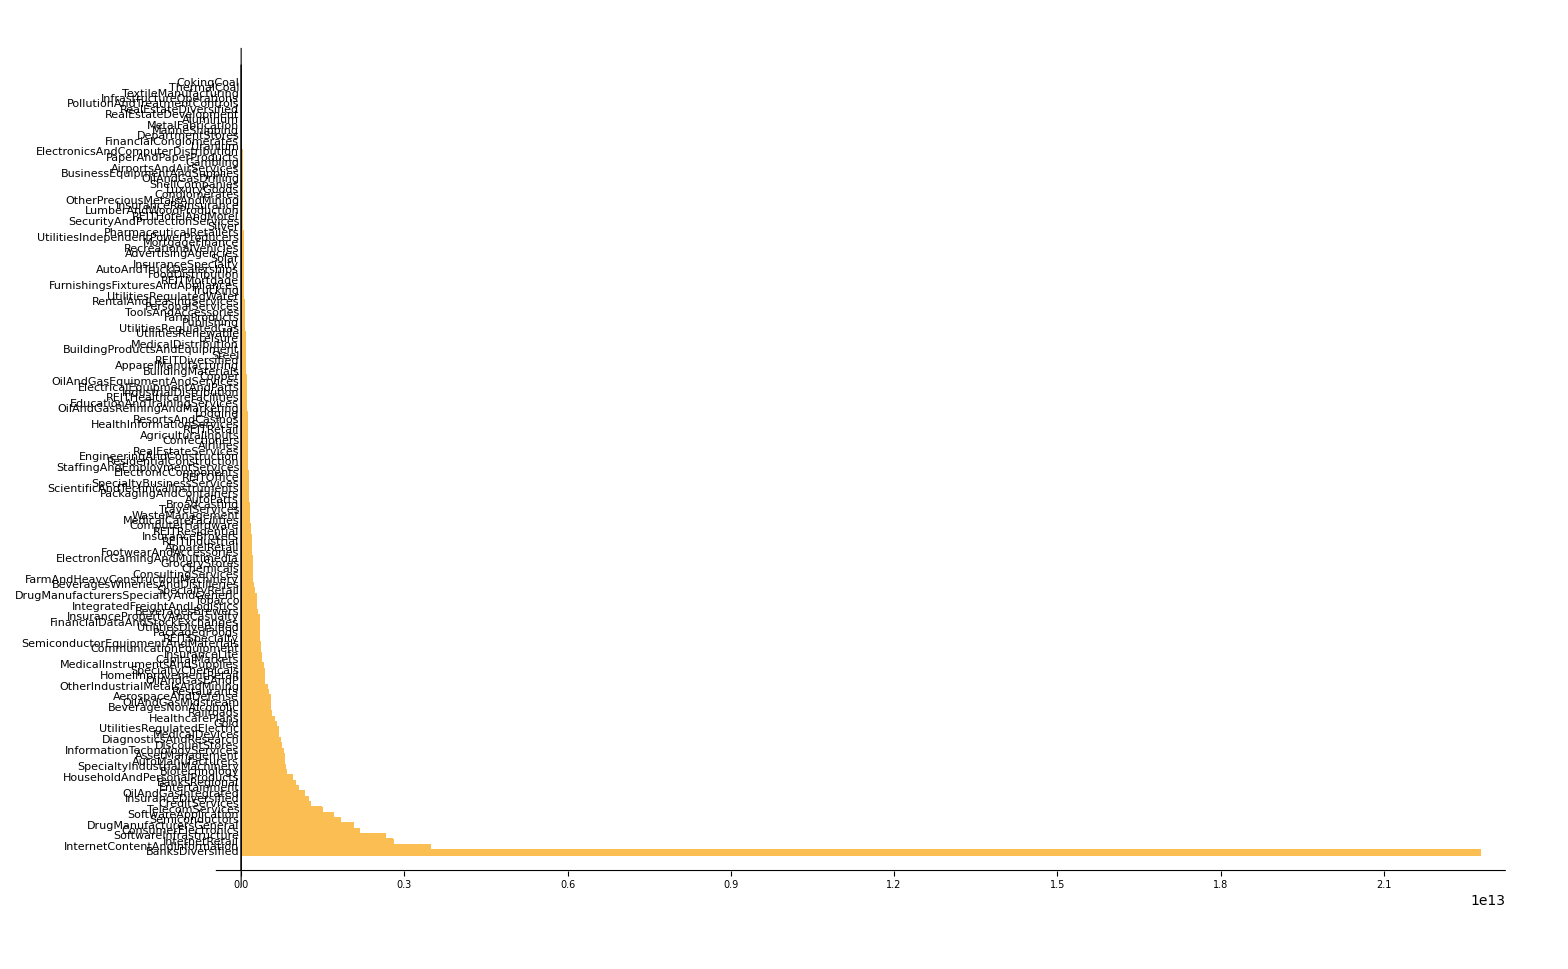

```mathematica
BarChart[Transpose[n2][[2]], BarOrigin->Left, ChartLabels->Transpose[n2][[1]],ImageSize->3000]
```

```mathematica
members[sector_]:=FinancialData[sector,"Members"]
```

```mathematica
(* Primero encontrar los instrumentos que tenían datos el 1 y 2 de enero de 2003 *)
```

```mathematica
dataprobe[sector_]:=DeleteCases[Transpose[{members[sector],FinancialData[#,{{2003,01,01},{2003,01,02}}]&/@members[sector]}],{_,_Missing}]
```

```mathematica
dataprobe["BanksDiversified"]
```

{{NASDAQ:EWBC,TimeSeries[…]},{NYSE:BAC,TimeSeries[…]},{NYSE:BBVA,TimeSeries[…]},{NYSE:BCS,TimeSeries[…]},{NYSE:BMO,TimeSeries[…]},{NYSE:BNS,TimeSeries[…]},{NYSE:C,TimeSeries[…]},{NYSE:CM,TimeSeries[…]},{NYSE:CS,TimeSeries[…]},{NYSE:HSBC,TimeSeries[…]},{NYSE:ING,TimeSeries[…]},{NYSE:JPM,TimeSeries[…]},{NYSE:MUFG,TimeSeries[…]},{NYSE:RY,TimeSeries[…]},{NYSE:SAN,TimeSeries[…]},{NYSE:SMFG,TimeSeries[…]},{NYSE:TD,TimeSeries[…]},{NYSE:UBS,TimeSeries[…]},{NYSE:WBK,TimeSeries[…]},{NYSE:WFC,TimeSeries[…]}}

```mathematica
(*Súper bien. Ahora hacemos un índice con todos los datos del dataprobe *)
```

```mathematica
dataprobe["BanksDiversified"][[1]]+dataprobe["BanksDiversified"][[2]]
```

{NASDAQ:EWBC+NYSE:BAC,TimeSeries[…]}

```mathematica
index[sector_]:=Total[FinancialData[#,{{2003,01,01},{2020,12,31}}]]&/@Transpose[dataprobe[sector][[1]]]/Length[dataprobe[sector]]
```

```mathematica
index["BanksDiversified"]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

FinancialData::notent: … is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

1/20 Transpose[TimeSeries[…]]

```mathematica
DateListPlot[%]
```

AbsoluteTime::arg: Argument «5467» cannot be interpreted as a date or time input.

DateString::arg: Argument DateObject[Max[-∞,TemporalData`InAbsoluteTime[AbsoluteTime[«5467»]]]] cannot be interpreted as a date or time input or as a date string format.

DateListPlot::ldata: … is not a valid dataset or list of datasets.

DateListPlot[1/20 Transpose[TemporalData[TimeSeries, <<1>>]]]